```mathematica
SetDirectory[NotebookDirectory[]];
β=0.1296;γ=2.70536;ep = 0.08;ρmax=0.25;
```

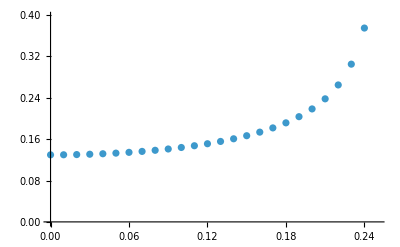

```mathematica
(*Siguiendo la idea de Ratas, vemos como cambian los valores 
de los parametros en la otra formulación, en particular 
el valor del nuevo beta crece cuando el valor del ρ asociado
a la fuente de alta frecuencia aumenta*)
lr={};br={};bhr={};
Do[
eqn=FindRoot[0==(-β+3ρ^2/2)v + (1+β)v^2-v^3 + (1+β)ρ^2/2-v/γ,{v,0}];
aux1={ρ,
((1+β-3v)+Sqrt[(1+β-3v)^2-4(β+3ρ^2/2-(1+β)v+3v^2)])/2}/.eqn;
AppendTo[lr,aux1]/.eqn;
aux2={ρ,
((1+β-3v)-Sqrt[(1+β-3v)^2-4(β+3ρ^2/2-(1+β)v+3v^2)])/2}/.eqn;
AppendTo[br,aux2];
aux3={ρ,
((1+β-3v)-Sqrt[(1+β-3v)^2-4(β+3ρ^2/2-(1+β)v+3v^2)])/((1+β-3v)+Sqrt[(1+β-3v)^2-4(β+3ρ^2/2-(1+β)v+3v^2)])}/.eqn;
AppendTo[bhr,aux3];
,{ρ,0,ρmax,0.01}]
g1=ListPlot[bhr];
g2=Plot[0.5,{ρ,0,ρmax},PlotStyle->{Black, Dashed}];
Show[g1,g2]
```

```mathematica
(*img1=Plot[{ld[δ],bd[δ]},{δ,0,0.3},PlotLegends->{"1(δ)","β(δ)"},Frame->True]
Export["Fig1.png",img1]
img2=Plot[{bd[δ]/ld[δ],γ (1+3δ)ld[δ]^2},{δ,0,0.3},PlotLegends->{"New β","New γ"},Frame->True]
Export["Fig2.png",img2]
img3=Plot[{(1+3δ)^2ld[δ]^4},{δ,0,0.3},PlotLegends->{"(1+3δ)^2 1(δ)^4"},Frame->True]
Export["Fig3.png",img3]*)
```